# The simulation when the cylinder rolls around on the ground

## Define equations

```mathematica
eq={
m2(x0''[t]+R(θ''[t]Cos[θ[t]]-θ'[t]^2 Sin[θ[t]]))==-f2[t] Cos[θ[t]]+Fn2[t] Sin[θ[t]],
m2 R(-θ''[t] Sin[θ[t]]-θ'[t]^2 Cos[θ[t]])==f2[t] Sin[θ[t]]+Fn2[t] Cos[θ[t]]-m2 g,
f2[t]-f1[t]==x0''[t]/R^2 i,
f1[t]+f2[t] Cos[θ[t]]-Fn2[t] Sin[θ[t]]==m1 x0''[t]
}
```

{m2 (x0''[t]+R (-Sin[θ[t]] θ'[t]^2+Cos[θ[t]] θ''[t]))==-Cos[θ[t]] f2[t]+Fn2[t] Sin[θ[t]],m2 R (-Cos[θ[t]] θ'[t]^2-Sin[θ[t]] θ''[t])==-g m2+Cos[θ[t]] Fn2[t]+f2[t] Sin[θ[t]],-f1[t]+f2[t]==(i x0''[t])/R^2,f1[t]+Cos[θ[t]] f2[t]-Fn2[t] Sin[θ[t]]==m1 x0''[t]}

## Define initial conditions

```mathematica
initial={x0[0]==0,x0'[0]==0,θ[0]==0,θ'[0]==0}
```

{x0[0]==0,x0'[0]==0,θ[0]==0,θ'[0]==0}

## Define parameters

```mathematica
params={m1->28.94,m2->1,g->9.8,i->2.7425,R->.788,wheeldiam->.038}
```

{m1→28.94,m2→1,g→9.8,i→2.7425,R→0.788,wheeldiam→0.038}

## Control equation

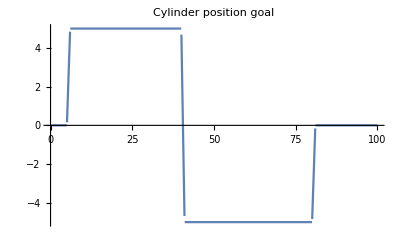

```mathematica
goal[t_]:=Piecewise[{{0,t<5},{0+5(t-5),t<6},{5,t<40},{5-10(t-40),t<41}, {-5,t<80},{-5+5(t-80),t<81}},0];
(*goal2[t_]:=InterpolatingFunction*)
Plot[{goal[t]},{t,0,100},PlotLabel->"Cylinder position goal"]
```

```mathematica
ceq={
motorspeed[t]==(R θ'[t]-x0'[t])/(wheeldiam*Pi) (* Rotations per second *),
command[t]==(wheeldiam/2)(10θ[t]+.695 θ'[t]+b (x0[t]-goal[t])+.725 x0'[t]),
torque[t]==command[t]/(.01 Abs@motorspeed[t]+1),
f2[t]==torque[t]/(wheeldiam/2)};
```

## Solve ODE

```mathematica
Manipulate[
sol=Quiet[NDSolveValue[{eq,initial,ceq}/.params/.b->bb,{x0,θ,motorspeed},{t,0,120},MaxSteps->Infinity],NDSolveValue::pdord],{bb,0,1}]
```

```mathematica
Dynamic@Plot[Evaluate[#[t]&/@sol],{t,0,120},PlotRange->All,PlotLegends->Automatic]
```

## Visualize results

```mathematica
SetDirectory[NotebookDirectory[]];
<<"visualization.m"
```

```mathematica
man=Manipulate[getBB8[sol[[1]][t],sol[[2]][t]],{t,0,120}]
```

Part::partd: Part specification None⟦1⟧ is longer than depth of object.

Part::partd: Part specification None⟦2⟧ is longer than depth of object.

Part::partd: Part specification None⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

Part::partd: Part specification None⟦1⟧ is longer than depth of object.

Part::partd: Part specification None⟦2⟧ is longer than depth of object.

Part::partd: Part specification None⟦1⟧ is longer than depth of object.

Part::partd: Part specification None⟦2⟧ is longer than depth of object.